I used Mathematica to work through several examples of discrete distributions. I used the most general cases possible. My focus on generalization meant I didn’t include the Bernoulli distribution or the geometric distribution, which are special cases of the the Binomial distribution and the negative binomial distribution, respectively.

## Binomial Distribution

What’s the probability you will have 110 heads out of 2 00 coin tosses?

```mathematica
Probability[x==110,x\[Distributed]BinomialDistribution[200,1/2]]
```

522222081148488803833122500948439092033029510866275025575/25108406941546723055343157692830665664409421777856138051584

```mathematica
NProbability[x==110,x\[Distributed]BinomialDistribution[200,1/2],WorkingPrecision->100]
```

0.02079869433231031517558728371841005445768414097750047505022048008924276263789036205146574846025135596

What’s the probability you will have between 96 and 108 heads out of 2 00 coin tosses?

```mathematica
Probability[96<=x<=108,x\[Distributed]BinomialDistribution[200,1/2]]
```

3911045678877858479058581704940733125002017822953426773745/6277101735386680763835789423207666416102355444464034512896

```mathematica
NProbability[96<=x<=108,x\[Distributed]BinomialDistribution[200,1/2],WorkingPrecision->100]
```

0.6230655235089846805722325124602419646326044754620131215351757111539208666562609916548872155987871016

### different value for p

The probability of getting 10 out of 70 sixes:

```mathematica
Probability[x==10,x\[Distributed]BinomialDistribution[70,1/6]]
```

43010790698981560264968493356718681752681732177734375/369400551818460155582338457473806922708916165381455872

```mathematica
NProbability[x==10,x\[Distributed]BinomialDistribution[70,1/6],WorkingPrecision->100]
```

0.1164340185396338386510498230883484677507515388618920536719888827877847141091800618609411721395454844

The probability of getting between 12 and 60 sixes:

```mathematica
Probability[12<=x<=60,x\[Distributed]BinomialDistribution[70,1/6]]
```

187259069812181268064657770604381223577766417255859375/369400551818460155582338457473806922708916165381455872

```mathematica
NProbability[12<=x<=60,x\[Distributed]BinomialDistribution[70,1/6],WorkingPrecision->100]
```

0.5069268816474554030716964137396395963756543473173258267098037954010037388889134982242586357972781571

### conditional probability

#### fair coin

Find the probability of getting between 96 and 108 heads while tossing a coin 200 times given that between 84 and 120 heads have been scored.

```mathematica
Probability[96<=x<=108\[Conditioned]84<=x<=120,x\[Distributed]BinomialDistribution[200,1/2]]
```

11628989391050479264/18449216239063865589

```mathematica
NProbability[96<=x<=108\[Conditioned]84<=x<=120,x\[Distributed]BinomialDistribution[200,1/2],WorkingPrecision->200]
```

0.63032430431530068809899692345637817699678328822688987423451234841065472237923289930818501311173802387652995237308570370405266806550877430295020304057231993751711686954627743054145416963699253655539679

#### dice

Find the probability of getting between 16 and 18 sixes when rolling a die 200 times given that between 14 and 20 sixes have been scored.

```mathematica
Probability[16<=x<=20\[Conditioned]14<=x<=20,x\[Distributed]BinomialDistribution[200,1/6]]
```

36193145699/36895670699

```mathematica
NProbability[16<=x<=20\[Conditioned]14<=x<=20,x\[Distributed]BinomialDistribution[200,1/6],WorkingPrecision->100]
```

0.9809591481414907345251618026427464239765872157997276145409582597597543675973819434483781302679606291

## NegativeBinomial

The number of tails before getting 150 heads with a fair coin is modeled by the negative binomial distribution with n=150 and p=0.5

```mathematica
𝒟=NegativeBinomialDistribution[150,1/2]
```

NegativeBinomialDistribution[150,1/2]

Make a picture:

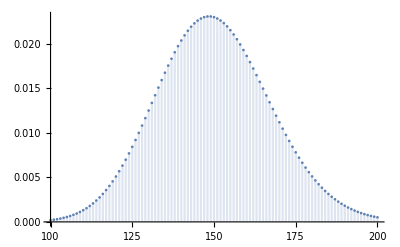

```mathematica
DiscretePlot[PDF[𝒟,k],{k,100,200},ImageSize->Full]
```

Find the probability of getting 144 tails before getting 150 heads:

```mathematica
Probability[x==144,x\[Distributed]𝒟]//TraditionalForm
```

177581905345755788536968927329795127320244431122016245473913189034720070489983603588925/7957171782556586274486115970349133441607298412757563479047423630290551952200534008528896

```mathematica
NProbability[x==144,x\[Distributed]𝒟,WorkingPrecision->150]//TraditionalForm
```

0.0223172139798520103824263061096657053816142787336076491498565735075784938534542633269142347429034257334133198806005769957272081553579779121349985105267

Find the probability of getting between 144 and 156 tails before getting 150 heads.

```mathematica
Probability[144<=x<=156,x\[Distributed]𝒟]//TraditionalForm
```

297857618329631577142510926472452399321226408704586048733051249882573754121758523794407601/1018517988167243043134222844204689080525734196832968125318070224677190649881668353091698688

```mathematica
NProbability[144<=x<=156,x\[Distributed]𝒟,WorkingPrecision->150]//TraditionalForm
```

0.292442177546227742645308199294917938042209286047821489985938298898894428661664174648671978500538827238572356679570434698803903729994502214511203952152

### dice

Investigate the behavior of probabilities until a 6 is rolled 60 times.

```mathematica
𝒟=NegativeBinomialDistribution[60,1/6]
```

NegativeBinomialDistribution[60,1/6]

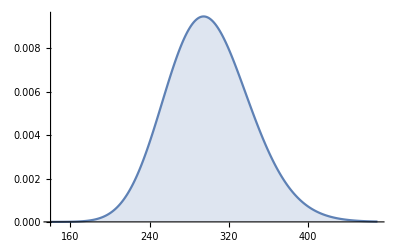

```mathematica
DiscretePlot[PDF[𝒟,k],{k,140,470},ImageSize->Full]
```

Find the average number of rolls needed:

```mathematica
Mean[𝒟]
```

300

Find the probability of needing between 200 rolls and 400 rolls:

```mathematica
Probability[200<=x<=400,x\[Distributed]𝒟]
```

242849610078700433727423260091307804908958805482793279992903925580985060007249275638245059816939076204344209823712956279197244662023245508432257459314383516923308246926820248309248839105935436958296992608018856652170435280643360462492005927256340569324965200292921634779677610620276774677485357970211393424650445408384535905810253098024986684322357177734375/247327652660853136657582802549317307860836151000010160928399335413303654526380251219029844833123749884079069365831121470556071608955707772005518141766714790551099190488887312922073823036667133302676745473036458705631169164059807664647218028456946038541560697004494042933305183130229545409376689763919078773176614442061950620827416361446140111920529057775616

```mathematica
NProbability[200<=x<=400,x\[Distributed]𝒟,WorkingPrecision->500]
```

0.98189429069505140434287598528484891128963732885686008207364192747761748771061299531151199914933059791381728947905891191068620822208529168615793247743602544957086609873587841720966327684300195785182919921609026743444823007962982097212460290810146668994562409081862048045025588032858546123925669948204154550459886645719441994784752015742900484369650404929141670369817216281284705102150277165953556508297351016995992873479608407157217177487860393179683876117527749286176452913264630079930304021728859269

Find the conditional probability of needing 300 rolls given between 200 rolls and 400 rolls are needed:

```mathematica
Probability[x==300\[Conditioned]200<=x<=400,x\[Distributed]𝒟]
```

7463668295930132726957016095102242169311620316559563760547457068240709453412729400212202779631081834290575807202532000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000/780488554937850496930875685014804054589907040883433468008920243582528877616919398404984410604811312307119145942088368203373069259725571799886875171235908504579453835240538389329910106082579702507763373334695136287579

```mathematica
NProbability[x==300\[Conditioned]200<=x<=400,x\[Distributed]𝒟,WorkingPrecision->500]
```

0.0095628158141594491129323341745967670009658079144085290734814635152263905858538358725361290684699469497491163437089394627858840317736058857301588738117342677394055355566440240526771007045414751017115812911559498615898256619724350814880446246821129177830588324502224683626017140180696683282944023148788826101377670908399829761114221479679761722794759547533732022418882565288290997380290786085067727141338848615766928281910854284778206687885985468335487827713254796472147383322052949554079423688118688703

## Pascal Distribution

Investigate the number of trials for the nth success.

If the probability a basketball player makes a free throw is 0.85 we can model this with a Pascal distribution.

```mathematica
85/100
```

17/20

```mathematica
ℬ=PascalDistribution[100,17/20]
```

PascalDistribution[100,17/20]

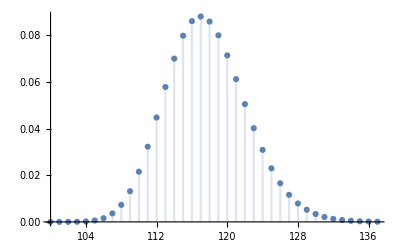

```mathematica
DiscretePlot[PDF[ℬ,x],{x,100,137},ImageSize->Full]
```

Find the probability he needs 108 free throws:

```mathematica
Probability[b==108,b\[Distributed]ℬ]
```

94857722905779789382123716687693390132920034611415847513701323124061536782762016595553918777744723325065677270318922136164936581757961153/12980742146337069071326240823050240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
NProbability[b==108,b\[Distributed]ℬ,WorkingPrecision->100]
```

0.007307573160025131931576501592780196109906675701569703221285782455514243977876551594998488264771416948

Find the probability he needs between 115 and 127 throws:

```mathematica
Probability[115<=b<=127,b\[Distributed]ℬ]
```

12340119534093950561648557166503532958037442796573068857769847640185176834520980936132602486066105356298060174804931766679109525061562926342387658387866907091167893/17014118346046923173168730371588410572800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
NProbability[115<=b<=127,b\[Distributed]ℬ,WorkingPrecision->100]
```

0.7252870400399598697061823206181459729880834426146601146442391480117582256236375838528338166383714723

Find the probability he needs between 16 and 18 throws given he makes 15 free throws within 15 to 20 free throws:

```mathematica
Probability[16<=b<=18\[Conditioned]15<=b<=20,b\[Distributed]PascalDistribution[15,17/20]]
```

828000/1220243

```mathematica
NProbability[16<=b<=18\[Conditioned]15<=b<=20,b\[Distributed]PascalDistribution[15,17/20],WorkingPrecision->100]
```

0.6785533701074294218446653658328709937282983799128534234574588831896597644895320030518511476812405398

Make a plot:

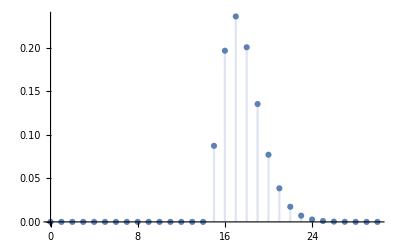

```mathematica
DiscretePlot[PDF[PascalDistribution[15,17/20],x],{x,0,30}]
```

Find the probability he needs between 22 and 24 throws given he makes 20 free throws within 20 to 26 free throws:

```mathematica
Probability[22<=b<=24\[Conditioned]20<=b<=26,b\[Distributed]PascalDistribution[20,17/20]]
```

46097100/75680867

```mathematica
NProbability[22<=b<=24\[Conditioned]20<=b<=26,b\[Distributed]PascalDistribution[20,17/20],WorkingPrecision->100]
```

0.6090984660627632608912897364138283458089876269520009595027498826090351211224892547808681948635710001

Make a plot:

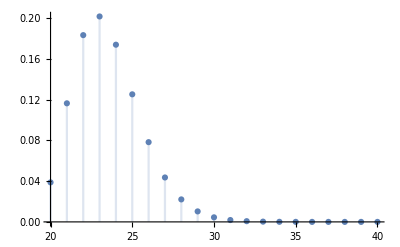

```mathematica
DiscretePlot[PDF[PascalDistribution[20,17/20],x],{x,20,40}]
```

Find the mean number of free throws needed.

```mathematica
Mean[PascalDistribution[20,17/20]]//N
```

23.5294

```mathematica
Mean[PascalDistribution[30,17/20]]//N
```

35.2941

Find the probability he needs 32 to 37 free throws to make 30 free throws if it is given he needs between 30 and 39 free throws:

This took a very long time to run so I am only evaluating it once:

```mathematica
Probability[32<=b<=37\[Conditioned]30<=b<=39,b\[Distributed]PascalDistribution[30,17/20]]
```

1303038921600/1580306483963

```mathematica
%//N
```

0.824548

## Hypergeometric Distribution Examples

### Hypergeometric distribution

There is an urn with 403 marbles in it. 148 of the marbles are white. 54 marbles are drawn from the urn.

```mathematica
urn[n_]=HypergeometricDistribution[n,148,403];
```

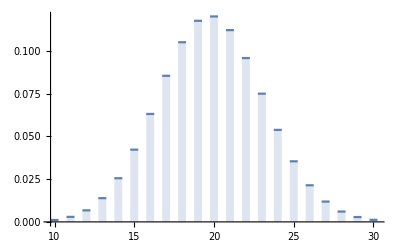

```mathematica
DiscretePlot[PDF[urn[54],k],{k,10,30},ExtentSize->1/2]
```

The probability distribution that there are 21 white marbles elements in a draw of 54 marbles:

```mathematica
PDF[urn[54],21]
```

4160984764936668505747373569589911437037308/37126596243372003987454725483769668696553919

```mathematica
Probability[WhiteMarbles==21,WhiteMarbles\[Distributed]urn[54]]
```

4160984764936668505747373569589911437037308/37126596243372003987454725483769668696553919

```mathematica
NProbability[WhiteMarbles==21,WhiteMarbles\[Distributed]urn[54],WorkingPrecision->40]
```

0.1120755788562089096845237920634821720275

The mean and variance:

```mathematica
Mean[urn[54]]
```

7992/403

```mathematica
Mean[urn[54]]//N
```

19.8313

```mathematica
Variance[urn[54]]
```

118541340/10881403

```mathematica
Variance[urn[54]]//N
```

10.8939

The probability there are between 18 and 20 white marbles given that there are between 17 and 22 white marbles in the sample of 54 marbles:

```mathematica
Probability[18<=WhiteMarbles<=20\[Conditioned]17<=WhiteMarbles<=22,WhiteMarbles\[Distributed]urn[54]]
```

25064549509/46516507129

```mathematica
NProbability[18<=WhiteMarbles<=20\[Conditioned]17<=WhiteMarbles<=22,WhiteMarbles\[Distributed]urn[54],WorkingPrecision->40]
```

0.5388312892773905762790102803722487983025

### Simple Wallenius Hypergeometric

Bob is catching fish in a small lake that contains a limited number of fish. There are different kinds of fish with different weights. The probability of catching a particular fish at a particular moment is proportional to its weight.

Bob is catching the fish one by one with a fishing rod. He is determined to catch exactly 12 fish regardless of how long it may take. He will stop after he has caught 12 fish even if he sees more fish that are tempting.

This scenario of the distribution of the types of fish caught is given by the Wallenius noncentral hypergeometric distribution.

The lake contains 10 red fish with a weight of 2 N and 15 blue fish with a weight of 12 N. Bob catches 12 fish.

```mathematica
𝒟=Block[{m1=10,m2=15,n=12,w1=1,w2=2},WalleniusHypergeometricDistribution[n,m1,m1+m2,w1/w2]];
```

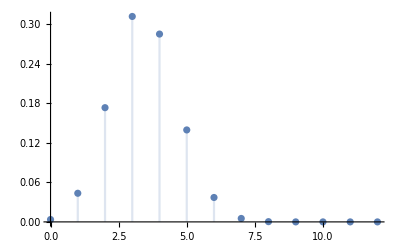

```mathematica
DiscretePlot[PDF[𝒟,x],{x,0,12}]
```

Find the probability at least 3 red fish were caught.

```mathematica
Probability[RedFish>=3,RedFish\[Distributed]𝒟]
```

1155705865/1482664962

```mathematica
NProbability[RedFish>=3,RedFish\[Distributed]𝒟,WorkingPrecision->100]
```

0.7794787727640386500210558020861897186992404289378492779139404792921787545418504332336141089708977691

Find the average number of red fish caught:

```mathematica
Mean[𝒟]
```

35869458643/10465870320

```mathematica
Mean[𝒟]//N[#,100]&
```

3.427279103053132422149102264053277510895051869895517681132513784099705909598925739412372157120326329

Simulate the number of red fish in 30 consecutive samples of 12:

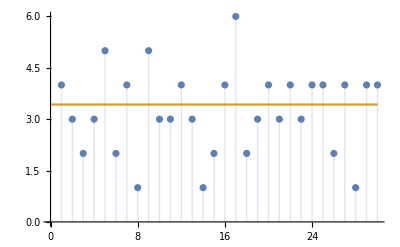

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->{1->Axis}]
```

### larger example of Wallenius Hypergeometric

Bob wants to catch 403 fish.

The lake contains 570 red fish with a weight of 3 N and 144 blue fish with a weight of 14 N.

```mathematica
𝒟=Block[{m1=570,m2=144,n=403,w1=3,w2=14},WalleniusHypergeometricDistribution[n,m1,m1+m2,w1/w2]];
```

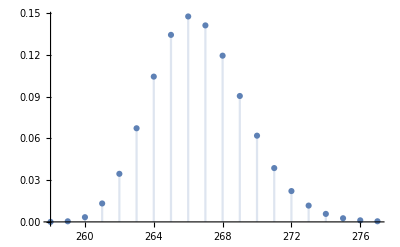

```mathematica
DiscretePlot[PDF[𝒟,x],{x,258,277}]
```

Find the probability at least 260 red fish were caught.

```mathematica
Probability[RedFish>=260,RedFish\[Distributed]𝒟]
```

293080649668889899284068726318069963032701968567369747664449674372964488547971950121144926723974483049487402292402194109389243354935991160244408607298544472990294776400153813183905708210928381667169626770433765479127771679451274900103500875208264736903586314581101473402167102477556252907561932803062283912539645637494929293363401167356298249074245034950878963783965149618729413919845288424709722386172149263141483468788800228986225822936306633166995682114770740002037167852060245997505846787001021501475817696120897704642673339568074514867224463155939828698405265160439126156212353302528145724164631769938372208310110996951297455733919593292759780002013308206706245845603960177634929604326487400873251047705178842745318292551468039684620857840663562371098907922885166834203844801303602440955070973868198965866832986486875555341378087478754643465474552067726090492041837750443655628543583714578786943236771859376993038513595946606791141724296123016666222892683253043354058619289143082026687505005977014793135784059479959314803291465009229309490101133426215935162977818241386990398151029273737208489211983488669292606159935981469691230810759249331615537511166208767058935546824917256608655121780827647832694180434742655618286064788403183273925767136811865960650206043436371978730712741704259270987604267031875653639489087771645700094066312301180480013028236522539414538682036327670233493787658169861900848957465200340216120085102426552791/293206145944026863765288880618440700493520452750354120107019223702913995122561310523279013762494617526946625334450592296283541568147527375753232647985601518604197998947690766754134643123778091709881065843976169257971363184959850002699545613043994730413795355078018121529159832982229290620186824836420098850094316461254689214372246318869875688113311498603053720054630268827301902552505346202488862531329630479766928891774084265716203658043265288376294525076807045754572648319650667378894014332822949503917094153111048613626502636213335467451836344568792155280096832809403734603205689422267076571222879393389908060208821750986629511341815209875679542934808911509014446243144773695353042448955223035744560379426436820539121020175239542776943997804058369122276583942742428235112410544379736684061894684212572107782408255750326748983970640638982195865128229143328446861719755202268471178994113066509013356281092706419138003025734757172484212849139065472165363173681986583679913779014333429893687128914193065378564911666846913018459562118726448228152903304521673850378159196404038856724950094170584764805405020910612622845243132657311409065499634042635116201130140500670865831447570878503824973835532811165343833523163651405490287611642943066350439713380651451931641840867719715326065598173644283473038178102217013733803410998435936212369526081579155683283643045675280404277319932189048792746332095131578582163177978366505374210747843956308500

```mathematica
NProbability[RedFish>=260,RedFish\[Distributed]𝒟,WorkingPrecision->100]
```

0.9995719862053610508026055638289927125435230747665575303257172319264955893857096110449966682596575205

Find the probability between 263 and 270 red fish were caught:

```mathematica
Probability[263<=RedFish<=270,RedFish\[Distributed]𝒟]
```

961547306361782394100135780931678036125128496557215643366745287322863682252106067032399112261890794335966782446401632204733581393109913167272784583799049149743598688378655476232082012603875598397169130452984573863799469107474445099117607422689560576093416782514197770612893331338952830054912080424794573187934400336358967581692316665806356309729032308930556069127757317318781447444392466970037761941468032476067464796921976219650502458688934322864991422891676080463990180176030715219813121718728104821313831560618259214255799369598373020614847704473059082449260846681521932680788806656161292573182778327161522587287011384427336550238247739052409235695971090533434004254708204023029539241842257801740354376801707330992655546673498330443646276515495220441502569582809620753193459082810908295498487716463950212755644246840030515425578048430123748513774349824912455444986892527627902378514796837396479355016444522159694719747412696291089135056595360479718131275665354588346430685728263621564433888507587601580732373844419928015963915938936615819974025307549367585267129983897099629563369855554158475360444719453434904356424067543005298594516443922307489256830224837193740928995303222988728027115680669200312986691496059106063362096626979380741809823352415753323606394360405061221771544240880196726814782933811823093528411115306908792904048416153773866388181212409835929693381381292884764205492937635952762107993298196754783681617359017579/1110587330642784334308454977265754937717941155748642683005003932324843071520951902325261922895639717966210148050433930954220445301612477704100728603241521069840067721435734944437899487624605775203216475493674277555100051901073955454954958083878917057151319653831113624670199842119953758938505913758383603139276637464326746395812928658538605495255301085423724671597270088350839331649695140162333714368531261521857182552487748813714393713625436969082350837838829159497148697454251293640820842134299574536487672920569245488108466708044361389127548385120149429269797016986682351277411672061808151556392318881790392676093330203768973703009131888783360533960188216577708044601632102833855255633408101249827492971051090969364321306253794365118382030086832596438720191980712833084989960902312327715142286831621372851351862709525772456978195236753756564381952049788442954118355629056079569636199381756463833889777971801800047911664208863309048270534633073782513538971410859568733943422928863607791236276007850408225692767042422729283174903669607613133071314265734919840460577166093243269095460236529709310267452911064139920120735773146105763902054607404758493659285781580537474663875955576557843375136574731403337411276440330050538359265951748674984379866294068164039081783354205338555589717108218816295404468945051674859758065924282617341474694104373571343176480041098279884860426302838785067633450653132410880162871559460272149704915224668125

```mathematica
NProbability[263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->400]
```

0.8658007162797897730766004810516498234119074203575403128097836147770559202243301757223195790447678380656624004964297680965332299585338040221283349263789410473617296802095580954879203663785390005882786719317918086418180160001288079482988700540864228475778215646078183219744322349701246306642607891160732899677111046405097809225710098960056105096663023954129639076671530060114691761617824169274819775573

Find the probability between 264 and 268 red fish were caught given between 263 and 270 fish were caught:

```mathematica
NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->1000]
```

0.6463378475216264030065819635244471734736956273586213410616800035264447199906946210443089700984366497374080814998979796368978897640617255056564350001812912211267259815273237139735068207698188913965962997724523042990265571991273188532306221325170290516642452887002136329821321042019553826009863501053632558489592388616514896740489966106706506235712209907121971517315858525699532052651050812402333989369065066854285426797200068280300088268953355316257492342224189929412920978391065621707119975514381252480389716835787095032152278576819600688128770536668426638979060977750693668343803110134345600315493397397271948454479247428901495507328597988231331929314290527124571176638712694769709201736906765965437662709425619137382731083475728958868371748567886236162357560661687580845754377707784482937351507931477258334201993071831919078081545764441881121618694320093245684791475700195927755639139502113583200622882098430684938016823505296960863268951070973349697563579249126738303976018632202349283576427639772

Form an approximate exact solution:

```mathematica
Rationalize[NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->1000],10^-1000]
```

104776836884695104286893053601437071514538170706108491421028766159855997652000137509486846143704495403638842047349144364285164173803869771791617054877713292259016698039430901116637323415639142441245901018252900221054964272264561217149519131354895158748133006062530608459180107959470941750705252628194180586059275631045917943513697598598795001747555918459662669155928120747178484776151116681408116539747020630597990352487066548862466513715224682275057775053244673599084762609299119217229558035576897965/162108465853362055010355114452158154720546081782712762466470364291074560437154788251428337290855925516798144144277062593386412893948241909925245792558987123777221779670251962087664431050796644582893556900240867322059684530791980149317638548188641935204568704076387448322252964009110524179624881219371042450433123370557677273716393922194860845943816026394040569703874609894684107698527220688800625717489430914477393598128922640986775787639982211398019248584911642430300334589276801754556673461393121286

Find a more accurate exact solution:

```mathematica
Rationalize[NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->1500],10^-1500]
```

613032982764178036402173827463100017602773261845623120711489466184442001742640701495845820412379435269608201872106669662158027683410864265629465630957655411813369187198517936442079284119837050743889267336186219909246432151422895077630256637420132630522459072662771320155042242310229272444462938391478527900010354795579913573524495695113591575539439360438389809053836873960264785688537536660932126813113208080323507896745456142876494314949591350241432348482163440164654599022692767598210415876604022784502937238295811675044145788256695901532788635898423729789611100875331109061350481842035991642314492733421143546298655116698606187461983203983422227834410311491534605955458863953548456571664523912596147936828796751397334639415457334988021562388174288/948471430405699723483995585431249271931444512749325274210939200224762185128771921527202228549362398827605690302140374583682934537712610988821445285325657234136064413044842056713442026889783953758426243623063391470098745332959198125295270123762989995384473911667105243749677133536829308232858715218911107506786386307016643409091770903727222265879079220428701797986721909160832607083700748376366643771767747866020889370913085601015655958138360231077339623180525828391890698113494904358894115422952902063976643142849837230676231316054468178594858997242084027289457074784145848990710652384261543069853126433143875460784958753324105646006192710779062929094513962928832256488018548138233597823267724333790181065941980463142531200264956286748469867864821057

Find the difference:

```mathematica
Rationalize[NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->1500],10^-1500]-Rationalize[NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->1000],10^-1000]
```

-(1751586736365941178568140895674836306479039080967324307858687376397772366117182039752993819633436644535507964789623066050180602611415868349460570541620314179354462719577110400466884737452163102648803883204096197914171328537915881680532638082581754637/153755248488811838394533906382723593563556277480280445564833938721014241954653467731510278225970708109359501548265076295981735530412667533977602176436936106453714421145899027967999653413609471195495590378102757000839175970644266313233779982013147272726019342632834381245964332502322306969899614437725427388144533470406134146639968358603275263386372438989718331796543459011939381878981131750326928256706933361440154281487551129606336559457715073020948757596326162754399865538472101207856467047430365859327715530160770182924783809316279301019083626220686780656895282742574096268786468953001749155200639827418389533130542808843399964230022240949941033168959574125141039898896335384181353287584446228201790988132116434245774286764797980757560075264453475236258604968966371006305405763049817780182521150083145131829435065904225005953823783441711478458763787021358235264413086922250940630400440548252426852869521589623249383328515812102181585270389104321577420170190054548732145355464183156897606889542618842720892014828570065726029269750034718657871252266036959079684791973726244321853246804720215893244670193298275136872413343041487001836671407646123033187365909606862987357999018943795042455704542514027228617577462065855033590452599828933136805087719302)

```mathematica
Rationalize[NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->1500],10^-1500]-Rationalize[NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->1000],10^-1000]//N[#,1000]&
```

-1.139204517297110167253972809081013518160894932263930832286251445348217441193829059797890865434940487876373546448343776889978253463569839894167990003166565714018528860059469016848949823484851813899452020207878812485312515806619758550680940440803930085231854061288556022296272993616936474131614952917265171052627993530991218178731236972250222964445302477083274061908886603217100955083767201767794127020595330276744741160188852001573264758934776467377724666067479543254597385004270306856854995804284960302934962191119254167625793588738033837075859431398618063704078020770336788202086917360940507901292407141529969238136268977260445946632850282920404006775503945924551470895770095233751487628058242814982104348295455396920610192381458068966996158194281142040507060925667186637987316462040146642466779745398086356490498669920445233798497096682468236610229355819865003659357477173308863264040074155538470048229275160919475300056744247523984911136756984491126835749110984088496197620008215658858875799703369×10^-1001

Please comment if you have any ideas on how to find the exact conditional probability for Wallenius noncentral hypergeometric distribution.

Find the average number of red fish caught:

```mathematica
Mean[𝒟]
```

2562721882021945273935552423289638978380853575362046001914347508970196492756426452026967505362852371768407654433426496590333501317521502519894824084416337290556115378215945756570887867463790797207824779899222787789125982571442320101718175661332726678607969219005690290464812882647806702816554257562598062995341043471037165318142348928360558842076145220249374869739862316107474119802762089596370035889876864028137220141703867728614817550869446486631828007617068529023681204402109929880937445993987431466784119770193386179643468389717200871254419662507157146052398860551233406303262478377640770986566320916362764897413022043730729962142955798740176912736120340258406254858774001624373341214156407508955921201995525572735868103947575011387726161594377962787840796504401109765546665869153346894810773835132728643774348697286449580038814694532891433113706756006748239056029010427177035556853988586425065565557522225588375197114201574818059089563195854966279847116804819395224371749266309389248947814305542358062080205517383108403360113201703103864340761729603344886020854804097183434521693577732556817642722236876968306082773222954942897047447769031555312088005348395407791357655504466220412550056811290295979538861451682986615936611788529273376954414116000046974509334192631874441357524169508179747183325651134863336496733965390113269994561105545784279032603512657592958746453242492809250796607982867857033555361664838882869307741287822653396731621490168773204610218885389734751285920687533082449332239/9611771445207769155336871027194752755072897276482225878839220633187483296792911122399648924371505054979060541638063804836916830885202165729328297648116637046347746247174925582148720692468764383845644442016737506408208256167676861590602410902216436811638753755109236960745813767595706582457308176381492456077570135590779104903649416490133093141706990270189255192375752119603585261318035236306792094069702115622525616183658640948316068208358703146693017196982056084551470213201081599646817912657933343776487045575353173464427880673684134537683795247376669257193933027371410615471321296204617181340443664830485993507635657219114178762095677602152462090666044880726182614334573605011366994188078543406329214798143992460455232468743364256198343852046239730425205972986416907979440614597500916579282928438469655552776468943173765628679763294652069576737497869413683053145636368180911076164346643860496950947685509181089453376935593684529123926547513931492736767105919858188884665371480918293202193638391522739282604121799733718198270301832733745976366030832868168431186236050648008128523561287979097225361678840462664024202448153214259379360410728316960041091885735930365553905592263260195675452768666792491483324751755318234256403568831034513243392101099895100014861940401201488165736020141222397112404393600831547579495903387736250174718251126502325179046124202912964265319637893951365783065430763817068123859794545755735636714413439989415809956743302991389018266642817013094598801425316784474430000

```mathematica
Mean[𝒟]//N[#,100]&
```

266.6232646740331624105809717002540336430673865987875701022154512267191750654823415590956085619225586

Find the variance:

```mathematica
Variance[𝒟]
```

210829688541117055742370356522311545227171406633600108097280857626646078530602928282008509399198979629210361338200043984026199702716443213428290309261708627839738275429438957414139775616663522693530494029294993286585984231760822327801369746435212441898496931262907069724077270179079919520101572843767584942196480938500085236771313987497537468513732645146520730090639400633175350410638963831967220958088659045576003685035568760276102594644619515468900109179093573953285909887265313772478840297811707126960830061316967851047015420901216364374875832785462429378040981609068455441347854944395215143546785127933573373489879841417626630393505425675279719097611608580546175192087528414569473384282165112571486143732640471121029363987120725677097831066117812529912911386730508525847955364804798244454292854634399651254020126980007992183022598676119883542967227920930731393482610688449772710228157685168093668840698101150084520910042980709529640085900308153254098342128472574780291049396124091313438492965354982991796761859109680234272738850810904343987193676753785704673318459910913487767823812497451760812942300038017412121399836484750721948472191874091771853786363001459392822176615034952044207689127178220214184211126459212344371984493228326196407812206157550553274241509326032302847265135431359310182843545811467457476959602284621517131642097625671913803360035689361377624053278603898089587414112717188772405551317429581727349129588544240317720940202437304340019216767282934903249568955975689155149672069990577745565076525259854278056735310954049809389105182784233167755857893548900848910876789133780595533873050248801176064289036947680640480630272079465166717585253482030688968399306906170559326948756395384625960601584427244841776932328404187100170204772606931148529753377515039606351361064621191651285877966508385498003066334795481187779957974934236033940559948517951011479843343996160772641917254705052388341286925901505479506659771568574206424605148983440503732318327568824422928104316059325965041146069847680758765202348261999410077274003858562191086750239136636548822384954792522076687704167278647121587137465395038143311583192714513161262743898101132129009530702406754815489543268286151903334432078503581535355500874191923725115991409848968190173293064549344895410550329620624738480245110473954607543192899208737211919999990688402745483271562027201798449927470707475536130272788623703392665445458217942893531709436674073554253729024263665654232557309182011329511618624799326324521411663399789499032772903921144604670945877391242805686927374965527451408711457472315319544164903787993291572523639240780085831213945856684247195913201280488132906465244808179849337672850810942607888036179414218110765252802802168504531099828135346875489194687678578525098610881444537212809329822267553658028234462223673635004986104733378275232467873382916396836710980618382008207420113834714838336572941274276747569663343488286924698614338426887440315868006295671743975492530375312065993823013354507273974409369/28732092747937460108396860570203271754697283923375940055935454777417267622585904057052552519976141340268117643165985911057094615658023202321448092713930017023462567919297528917324116075859261714321302692255249063937556516066512133614910532019578375842665103777534454494282577250483073897024182786246105341322882099751154223404032102974836136742338967299604012713094762856680349710422287406437150090157362572921358324767411261202791210834998210409745318405412960589121775350351480747558143276956766683944963429908660493641550365393544136595273341206017776100483684531877199823076594274690736405099970479872950969928305772154495573250875237062165209160340504433415205371933190358834409991691364509828483896253448369973427501462092067357652545069229121975890509117786841010762361157261464018760814284695051842090007780748040559410816947558764909577058487471978035954838039723191255033061667120953417865007520369326826778115325460282995783376688755105717413228109755342169213591969748686010794037834090825501662828792813555850797068965689702252404356948703854174473912613867174958763540115915308988912798947570512355760510769227216980653277607550539782891601194531481591038533359429276711167398610344307272771648628753902848967109754874040318526745698107108981412414489629653342874067766162867731011892105335686759833941927118974194603053656575915564574868366941655008339318145704696550795876669833368750827557968367655382491092547576277750131734054881657335116336015066328018302327087430263396208440595037024248020388995049365664299084316451957553100763933548543468574443889266318289395806118752183732606837781919007273505397401705055277568653876292304618018782998716144220766277182795834837376070486708587037945031584052713742369929132976279023078547425169867475952935940405716835485648283593657723074515618965913392465786252925337308305378673539024924201230383863946507135684785108835144805680884804252029396381284281791447880244777642418135715407140773274300990071544127655069622190115216578828232180441367758370771842683504674577030875119179201499864881571367123648158616433944878062951984117049003547660381968596071131975891641196883548799921326441104257900713951214519527131907128314107437425291105421706639925424773913997971847392981659769421937563037837290302291093178454742685642824931874971664399824316579645023819216381909743230454850802612714464644925157327311723964096382677779857637707120639215089997770678010191956555582065246986414994291804149942019969996496166285347648515707750430629568199251638881296103487277134892987324540243088204399757327809326110975556554518960419660883156908054945304483047937903997014325718139248871656746635037170277433568185693602601096715751378294788682967055159345095535731925965462461294701185727763135828973792013354431812685237912068725065260617492188657095672087936100812885068495860019780743622569598289068926280438896607862816609590593796625170144734692534305714296383350159948762028494781004329656758800325035066929956438106201709543900000000

```mathematica
Variance[𝒟]//N[#,200]&
```

7.3377769726241578231051269177734952263284806520005346341994039775333855340079517054282703309586017703471925125414194642273989519224340688217118886871256722960623673034641844795753691956430159561293772

Simulate 30 catches of fish:

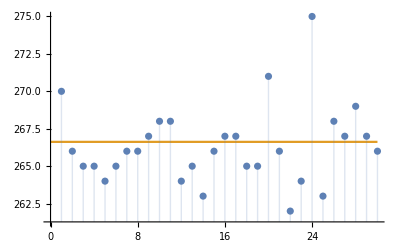

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->{1->Axis}]
```

The cases above could also be interpreted as marbles in an urn, for example.

Find the second moment:

```mathematica
Moment[𝒟,2]
```

2534338801691221888990925616158860184254513365724318951158519147362009287960866169945641633088171552285062123135419199374106570918351396112613288881300222606526921245491739571494645181216877842556821768328444086763815268097318213877204141451887144262271425294684992266633555272147712103324236425011706451503455218579008331356328643024083799810359072575393237431648491525850116974197865474115205159545454591907281258097681643841873794711819887661414856735424991221993398513900499234811934232755556821875880634614956263662179111509834247007964378787190633926317054520892839082545992729010110270142264315157273555087732117560629532593508471592656635152449136541487603592485062288250310914838873019797305359580190282215837234290794729886199417786554718854617951008000315757273420700323760770737869118713944001708023264021327085383119277800469458607037755518669473487421503804754180543207388021252196664158877329184419784900446316073222776521945311167485202840421203579197804654158724734287949950832574316012556648707449798111599859604168493838539815060610974092095019585195593634898819393723810115219292240683912364389015980244690413534637950833030236581023290126282326251527448714391030166859953276005924694781947180840762505714459850633402189572100324176994777691804539154979778856782261890686562398044047430938894470394939789583689625282591908220898938477940204582471785515459328232036573727015361676220920525325103981501886581629772381582883739649421093014374412427178993052287430943937678729381435801/35647063775497978622092620487568955277331682062865086436512748413030921869025839034862071053418682290782648720862120788977798877064880945132449240170272434156557144088756069833624812517043441334977798893135328026321412902345881648522557833959327398533113401916308021914043673887659034463389369505932724151415451763511288094336021771207870091600504459656221479648725745084117555560288522503304746829284057079574511527141098571285322113270182106900086368718619993349350171472127350327821333212702420595232388923709614750650867966314498059435328146939589453105470514822125316711892787839586800006436364324252074970811112139294738615272712589676125911365212912615572230922327711649249993094288666080060611074302486322975146577656651284473158082735783073071781385695385740389559186061292605613957579105980491380133550890782434902510452887039961764000949800445849383316351022782844707687921265151080582388778724622635829199321275617463747704920091887272333369577495038383777175326258456489138502854430627504264767000294988109547730212005263818338995824274485781946634910452951040398118902543311636277103257878766077035060798517256469237936742102479635471907081831766815001381350041494237557045077814970370108959451421756946841526730101099083705844743788917328164791063789188101600914492871971790730006310672689966403885115130621979244685454229475971996447671912077924230333221212427823038006360209153031954524093309584514883272789230083231615363331908297465509186995709391205292915827432563270529530000

I think more research is needed on the Wallenius noncentral hypergeometric distribution.

### Simple Fisher hypergeometric

You are catching fish as in the example with Bob, but using a big net. You set up the net one day and come back the next day to remove the net. You count how many fish you have caught and then you go home regardless of how many fish you have caught. Each fish has a probability of being ensnared that is proportional to its weight but independent of what happens to the other fish.

The total number of fish that will be caught in this scenario is not known in advance. The expected number of fish caught is therefore described by multiple binomial distributions, one for each kind of fish.

After the fish have been counted, the total number n of fish is known. The probability distribution when n is known (but the number of each type is not known yet) is Fisher’s noncentral hypergeometric distribution.

```mathematica
𝒟=Block[{m1=10,m2=15,n=12,w1=1,w2=2},FisherHypergeometricDistribution[n,m1,m1+m2,w1/w2]];
```

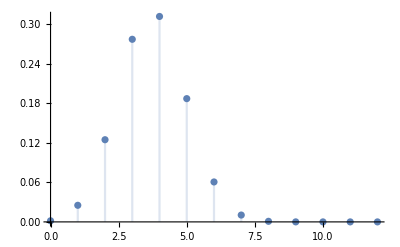

```mathematica
DiscretePlot[PDF[𝒟,x],{x,0,12}]
```

Find the probability at least 3 red fish were caught.

```mathematica
Probability[RedFish>=3,RedFish\[Distributed]𝒟]
```

6720275/7921683

```mathematica
NProbability[RedFish>=3,RedFish\[Distributed]𝒟,WorkingPrecision->100]
```

0.8483392986061169072279211374653593182155862586271124456760009205114620213911614488991796313990347758

Find the average number of red fish caught:

```mathematica
Mean[𝒟]
```

3286802/880187

```mathematica
Mean[𝒟]//N[#,100]&
```

3.734208753367182201055003084571801219513580636841943814212207178701798595071274626869063051374310232

Simulate the number of red fish in 30 consecutive samples of 12:

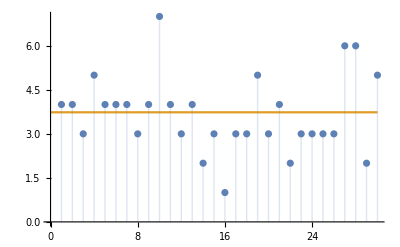

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->{1->Axis}]
```

Compute the variance:

```mathematica
Variance[𝒟]
```

1160420233804/774729154969

```mathematica
Variance[𝒟]//N[#,40]&
```

1.49783989199481338307429415751793040354

Compute a conditional probability

```mathematica
Probability[3<=RedFish<=5\[Conditioned]2<=RedFish<=7,RedFish\[Distributed]𝒟]
```

448/561

```mathematica
NProbability[3<=RedFish<=5\[Conditioned]2<=RedFish<=7,RedFish\[Distributed]𝒟,WorkingPrecision->40]
```

0.7985739750445632798573975044563279857398

Do another simulation of 30 consecutive samples of 12:

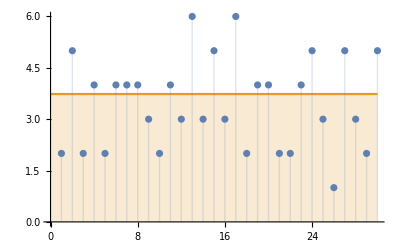

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->Axis]
```

### Multivariate hypergeometric

An urn contains 12 red glass marbles, 23 blue glass marbles, 11 yellow glass marbles and 9 green glass marbles. Find the distribution of a sample of 28 marbles drawn without replacement:

```mathematica
𝒟=MultivariateHypergeometricDistribution[28,{12,23,11,9}]
```

MultivariateHypergeometricDistribution[28,{12,23,11,9}]

Find the probability of observing between 5 and 8 red marbles, 3 and 10 blue marbles, 4 and 7 yellow marbles, and 4 and 7 green marbles in an urn with 12 red, 23 blue, 11 yellow, and 9 green with a sample size of 28:

```mathematica
Probability[And[5<=RedGlassMarble<=8,3<=BlueGlassMarble<=10,4<=YellowGlassMarble<=7,4<=GreenGlassMarble<=7],{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

376627430916/2483341104143

Find the probability of observing between 6 and 8 red marbles given that there between 5 and 10 red marbles are observed, 3 and 10 blue marbles, 4 and 7 yellow marbles, and 4 and 7 green marbles in an urn with 12 red, 23 blue, 11 yellow, and 9 green with a sample size of 28:

```mathematica
Probability[6<=RedGlassMarble<=8\[Conditioned]5<=RedGlassMarble<=10&&3<=BlueGlassMarble<=10&&4<=YellowGlassMarble<=7,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

3068729643/4007267641

Find the covariance matrix of the distribution:

```mathematica
Covariance[𝒟]//MatrixForm
```

(7224/3025 | -3864/3025 | -168/275 | -1512/3025
-3864/3025 | 10304/3025 | -322/275 | -2898/3025
-168/275 | -322/275 | 56/25 | -126/275
-1512/3025 | -2898/3025 | -126/275 | 5796/3025)

## Beta binomial

I will now work through an example with the beta binomial distribution based on an example from the documentation. There is an urn with two colors of marbles. There are white colored marbles and black marbles. There are w white marbles in the urn and b black marbles in the urn. A marble is taken out of the urn and observed. Then c more marbles of the same color are added to the urn. This process continues n times. That is we conduct n draws from the urn. This can modeled with the Polyà-Eggenberg urn model distribution.

This example function is from the documentation for Beta Binomial. I added checks to make sure the arguments are integers.

```mathematica
PolyaEggenbergDistribution[w_?IntegerQ,b_?IntegerQ,c_?IntegerQ,n_?IntegerQ]:=BetaBinomialDistribution[w/c,b/c,n]
```

I will use an example with 30 white marbles and 20 black marbles. Then I will conduct the experiment 15 times. Each time I will place 2 marbles back in the urn:

```mathematica
𝒟=PolyaEggenbergDistribution[30,20,2,15]
```

BetaBinomialDistribution[15,10,15]

Find the mean and variance:

```mathematica
Mean[𝒟]
```

9

```mathematica
Variance[𝒟]
```

72/13

```mathematica
Variance[𝒟]//N
```

5.53846

Find a conditional probability:

```mathematica
Probability[7<=p<=11\[Conditioned]5<=p<=13,p\[Distributed]𝒟]
```

2489227/3359841

```mathematica
NProbability[7<=p<=11\[Conditioned]5<=p<=13,p\[Distributed]𝒟,WorkingPrecision->40]
```

0.7408764283786048208828929702328175648788